```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g- t- t (1-loop)

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA} initialized

in total: 2 Particles insertions

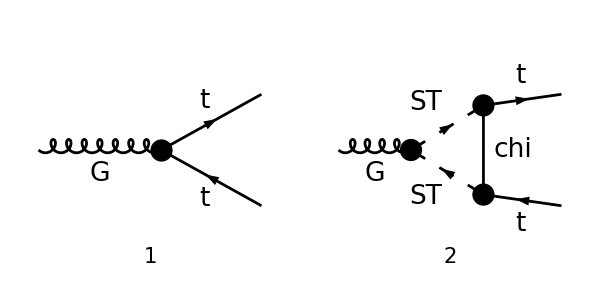

```mathematica
tops0 = CreateTopologies[0,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
tops = CreateTopologies[1,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],S[1],S[2],S[3],V[2],V[3],F[7],F[6],F[5],F[8],F[9]}];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 600,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

in total: 2 Particles amplitudes

-gs T_Col2Col3^Glu1 ((yDM^2 (p1^Lor1+p2^Lor1-2 q^Lor1) ((γ·p1).(γ̄)^6-(γ·q).(γ̄)^6))/((q^2-mST^2).((p1-q)^2-mChi^2).((p1+p2-q)^2-mST^2))+ⅈ (2 π^2 deltaCTL yDM^2+1) γ^Lor1.(γ̄)^7+ⅈ (2 π^2 deltaCTR yDM^2+1) γ^Lor1.(γ̄)^6)

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify)/.{LorentzIndex[a_,D]->LorentzIndex[μ,D]}
```

-ⅈ gs T_Col2Col3^Glu1 (2 π^2 yDM^2 γ^μ.(γ̄)^6 C_00(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+π^2 yDM^2 (p1^μ-p2^μ) (γ·p1).(γ̄)^6 C_1(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+2 π^2 yDM^2 p1^μ (γ·p1).(γ̄)^6 C_11(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)-2 π^2 yDM^2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6) C_12(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)-π^2 yDM^2 (p1^μ-p2^μ) (γ·p2).(γ̄)^6 C_2(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+2 π^2 yDM^2 p2^μ (γ·p2).(γ̄)^6 C_22(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+γ^μ.((γ̄)^6+(γ̄)^7)+2 π^2 deltaCTL yDM^2 γ^μ.(γ̄)^7+2 π^2 deltaCTR yDM^2 γ^μ.(γ̄)^6)

```mathematica
(* Remove SM contribution *)
ampSM=gs SeriesCoefficient[ampC,{gs,0,1},{yDM,0,0}];
ampC=Simplify[ampC-ampSM];
```

```mathematica
moms=Cases2[ampC,DiracGamma]
pairs=Cases2[ampC,Pair]
```

{(γ̄)^6,(γ̄)^7,γ^μ,γ·p1,γ·p2}

{p1^μ,p2^μ,p1^2,p1·p2,p2^2}

```mathematica
ampEsimp2=ExpandScalarProduct[DiracSimplify[ampC/.{DiracGamma[7]->1-DiracGamma[6]}]];
```

```mathematica
ampEsimp3=Collect[ampEsimp2//.{PaVe[0,0,a_,b_,c_,d_]->C00,PaVe[1,1,a_,b_,c_,d_]->C11,PaVe[2,2,a_,b_,c_,d_]->C22,PaVe[1,2,a_,b_,c_,d_]->C12,PaVe[1,a_,b_,c_,d_]->C1,PaVe[2,a_,b_,c_,d_]->C2},moms,DiracSimplify];
```

### Coefficients for each term

```mathematica
Table[{moms[[i]].moms[[1]],FullSimplify[Coefficient[ampEsimp3,moms[[i]].moms[[1]]]]},{i,1,Length[moms]}]
```

((γ̄)^6.(γ̄)^6 | 0
(γ̄)^7.(γ̄)^6 | 0
γ^μ.(γ̄)^6 | -2 ⅈ π^2 gs yDM^2 (C00-deltaCTL+deltaCTR) T_Col2Col3^Glu1
(γ·p1).(γ̄)^6 | -ⅈ π^2 gs yDM^2 T_Col2Col3^Glu1 ((C1+2 C11) p1^μ-(C1+2 C12) p2^μ)
(γ·p2).(γ̄)^6 | ⅈ π^2 gs yDM^2 T_Col2Col3^Glu1 ((2 C12+C2) p1^μ-(C2+2 C22) p2^μ))